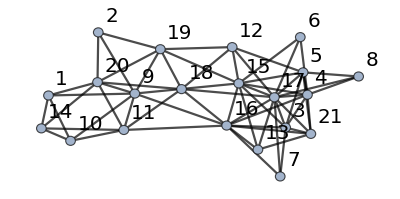

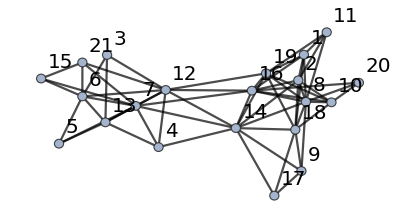

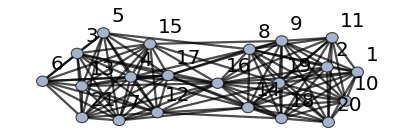

```mathematica
G1=System`Graph[{1<->9,1<->10,1<->14,1<->20,2<->9,2<->19,2<->20,3<->4,3<->5,3<->7,3<->15,3<->16,3<->17,3<->21,4<->5,4<->6,4<->8,4<->15,4<->16,4<->17,4<->21,5<->8,5<->12,5<->15,5<->17,5<->21,6<->15,6<->17,7<->16,7<->17,8<->17,9<->10,9<->11,9<->15,9<->16,9<->19,9<->20,10<->11,10<->14,11<->14,11<->16,11<->18,11<->20,12<->15,12<->17,12<->18,12<->19,13<->15,13<->16,13<->17,13<->21,14<->20,15<->16,15<->17,15<->19,16<->17,16<->18,16<->21,17<->18,17<->21,18<->19,18<->20,19<->20},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
G2=System`Graph[{1<->2,1<->8,1<->11,1<->16,1<->18,1<->19,2<->8,2<->10,2<->11,2<->14,2<->16,2<->18,3<->6,3<->12,3<->13,4<->7,4<->12,4<->13,4<->14,5<->6,5<->7,5<->13,6<->7,6<->12,6<->13,6<->15,6<->21,7<->12,7<->13,7<->14,7<->15,7<->16,7<->21,8<->9,8<->10,8<->11,8<->14,8<->16,8<->18,8<->19,8<->20,9<->14,9<->17,9<->18,10<->16,10<->18,10<->19,10<->20,11<->19,12<->13,12<->14,12<->16,12<->19,12<->21,14<->16,14<->17,14<->18,14<->19,15<->21,16<->19,16<->20,17<->18,18<->19},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNION=GraphUnion[G1,G2,VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNIONComplement=GraphComplement[GUNION,VertexLabels->"Name",VertexSize->0.1,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}];
```

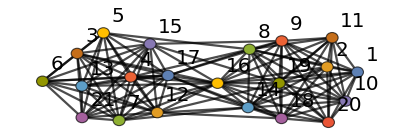

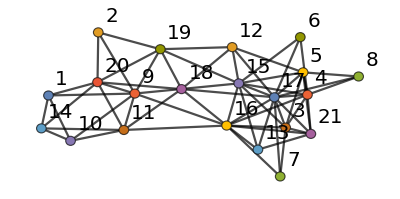

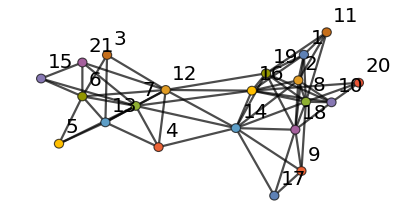

```mathematica
mvc={1,2,6,4,8,10,3,3,4,5,6,2,7,7,5,8,1,9,10,11,9};
GUNIONCOLORED=SetProperty[GUNION,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G1=SetProperty[G1,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G2=SetProperty[G2,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
Export["1.eps",G1];
Export["2.eps",G2];
```

1  40

2  41

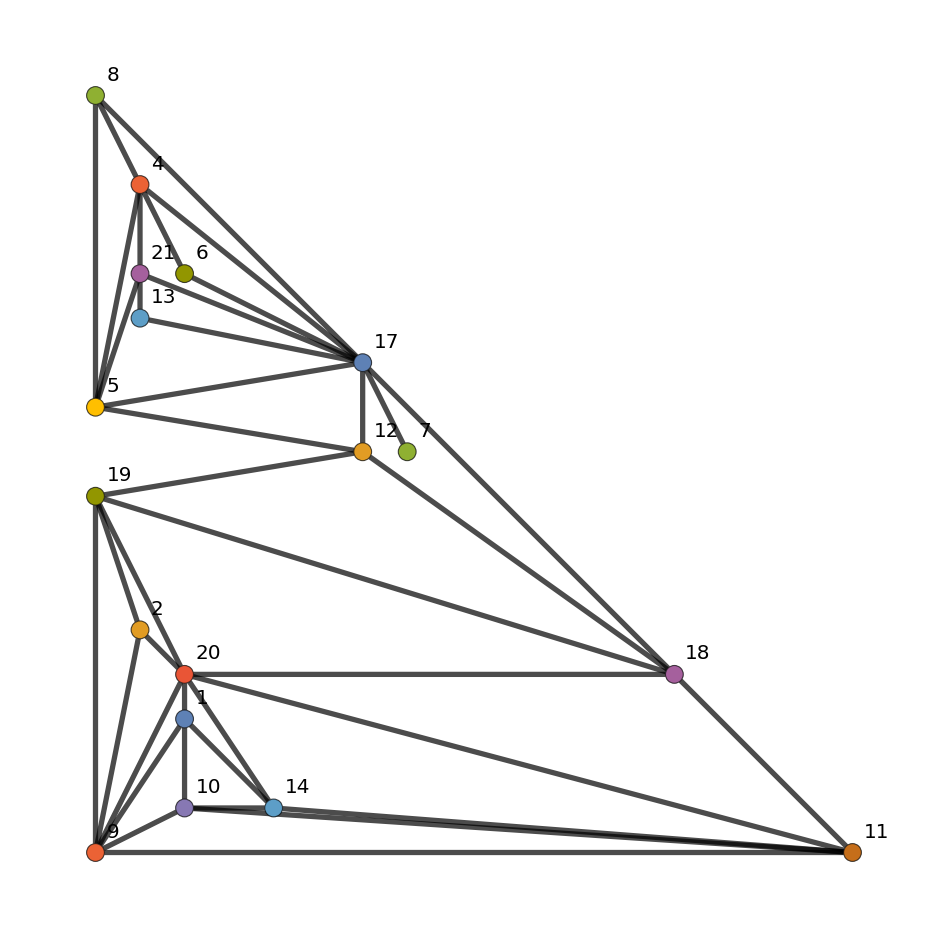
3 -Graphics- 39

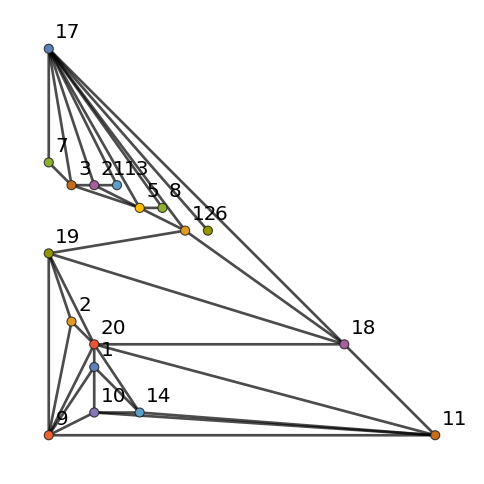
4 -Graphics- 38

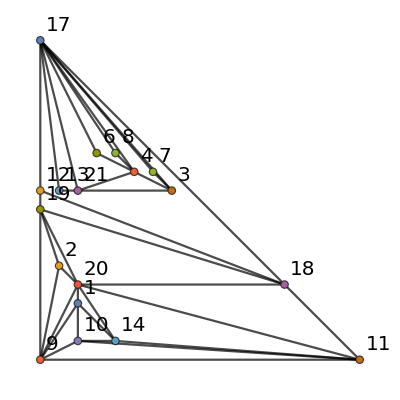
5 -Graphics- 38

6  42

7  42

8  41

9  38

10  40

11  39

12  40

13  42

14  40

VertexDelete::inv: The argument {15,16,15} in VertexDelete[Graph[<21>, <63>], {15, 16, 15}] is not a valid vertex.

SetProperty::pvobj: … is not an object with properties.

EdgeCount::graph: A graph object is expected at position 1 in ….

15 SetProperty[VertexDelete[-Graphics-,{15,16,15}],GraphLayout→PlanarEmbedding] EdgeCount[SetProperty[VertexDelete[-Graphics-,{15,16,15}],GraphLayout→PlanarEmbedding]]

VertexDelete::inv: The argument {16,16,15} in VertexDelete[Graph[<21>, <63>], {16, 16, 15}] is not a valid vertex.

SetProperty::pvobj: … is not an object with properties.

EdgeCount::graph: A graph object is expected at position 1 in ….

16 SetProperty[VertexDelete[-Graphics-,{16,16,15}],GraphLayout→PlanarEmbedding] EdgeCount[SetProperty[VertexDelete[-Graphics-,{16,16,15}],GraphLayout→PlanarEmbedding]]

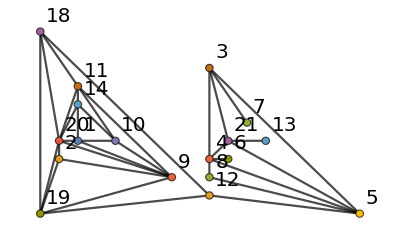
17 -Graphics- 34

18  39

19  39

20  37

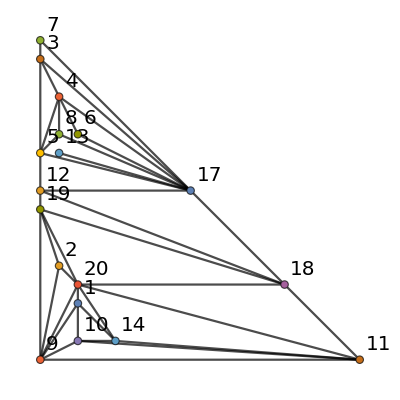
21 -Graphics- 39

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[A=SetProperty[VertexDelete[G1,{i,16,15}],GraphLayout->"PlanarEmbedding"];Print[i," ",A," ", EdgeCount[A]],{i,1,VertexCount[G1]}]
```

```mathematica
Table[PropertyValue[{MyDraw,n},VertexCoordinates],{n,1,19}]
EdgeList[MyDraw]
```

{{0.,0.},{9.,2.},{6.,2.},{10.,5.},{2.,5.},{10.,2.},{5.,3.},{1.,3.},{9.,7.},{0.,10.},{12.,3.},{9.,1.},{4.,3.},$Failed,$Failed,{7.,2.},{10.,3.},{3.,4.},{16.,0.}}

{1<->3,1<->8,1<->10,1<->12,2<->4,2<->6,2<->9,2<->12,2<->17,2<->19,3<->7,3<->8,3<->10,3<->12,3<->13,3<->16,4<->9,4<->11,4<->17,5<->8,5<->10,5<->18,6<->17,6<->19,7<->10,7<->13,8<->10,8<->13,8<->18,9<->11,9<->19,10<->12,10<->13,10<->16,10<->18,11<->17,11<->19,12<->16,12<->19,13<->18,17<->19}

1  39

2  41

3  40

4  38

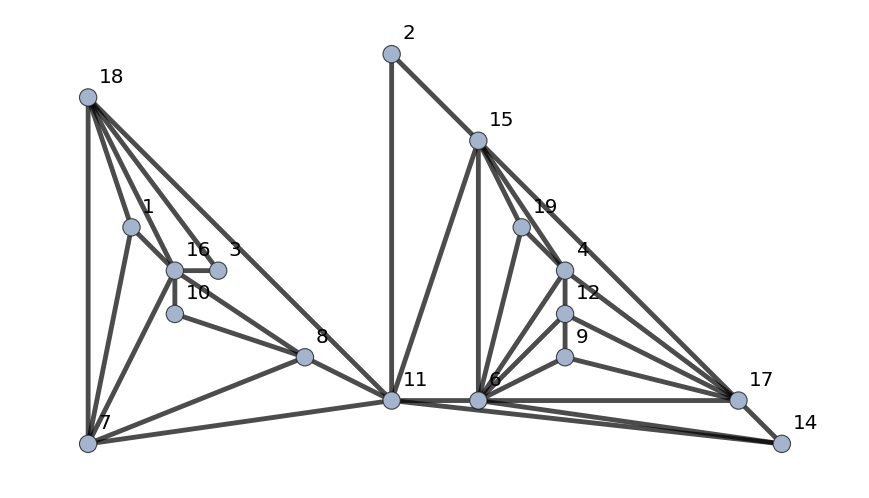
5 -Graphics- 37

6  35

7  37

8  39

9  40

10  41

11  35

12  39

VertexDelete::inv: The argument {13,13} in VertexDelete[Graph[<19>, <48>], {13, 13}] is not a valid vertex.

SetProperty::pvobj: … is not an object with properties.

EdgeCount::graph: A graph object is expected at position 1 in ….

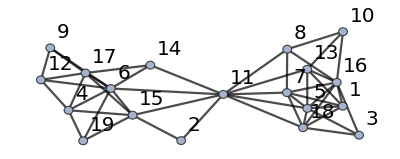
13 SetProperty[VertexDelete[-Graphics-,{13,13}],GraphLayout→PlanarEmbedding] EdgeCount[SetProperty[VertexDelete[-Graphics-,{13,13}],GraphLayout→PlanarEmbedding]]

14  40

15  37

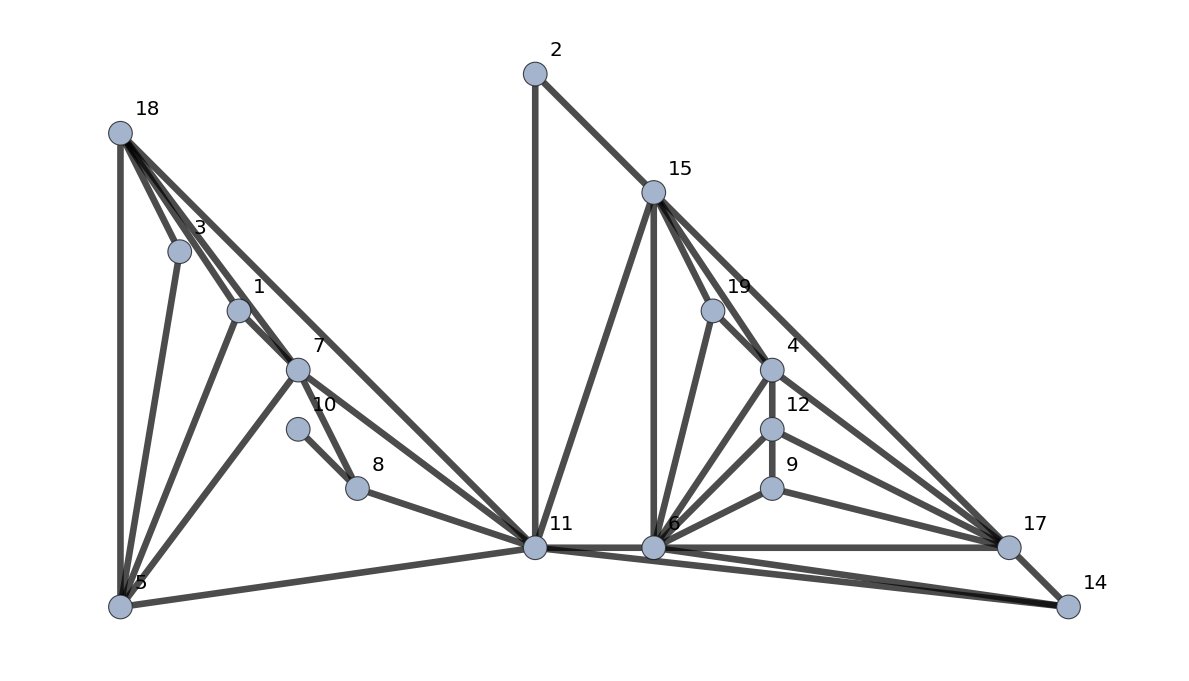
16 -Graphics- 36

17  37

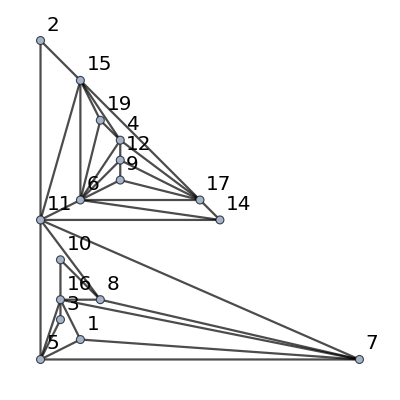
18 -Graphics- 37

19  40

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[A=SetProperty[VertexDelete[G2,{i,13}],GraphLayout->"PlanarEmbedding"];Print[i," ",A," ", EdgeCount[A]],{i,1,VertexCount[G2]}]
```

```mathematica
VertexCount[G1]
```

21